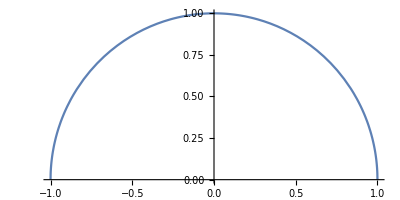

```mathematica
upper=Plot[Sqrt[1-x^2],{x,-1,1},AspectRatio->Automatic]
```

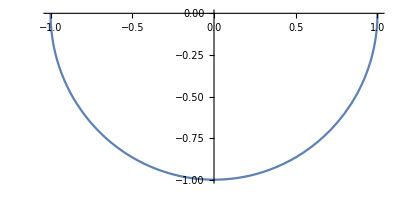

```mathematica
lower=Plot[-Sqrt[1-x^2],{x,-1,1},AspectRatio->Automatic]
```

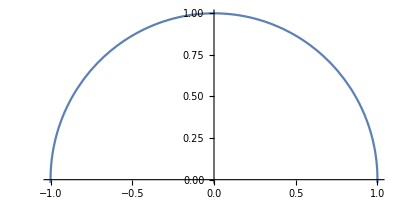

```mathematica
Show[upper,lower]
```

```mathematica
x[t_]=Cos[t];
y[t_]=Sin[t];
f[t_]={x[t],y[t]}
```

{Cos[t],Sin[t]}



```mathematica
ParametricPlot[f[t],{t,0,2Pi},AspectRatio->Automatic]
```

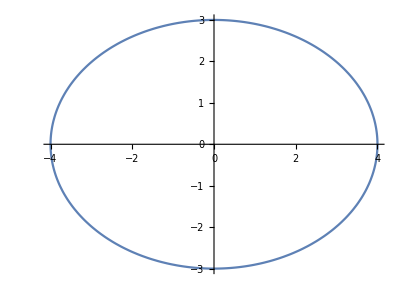

```mathematica
ParametricPlot[{4Cos[t],3Sin[t]},{t,0,2Pi},AspectRatio->Automatic]
```

{1+3 Cos[t],-2+3 Sin[t]}

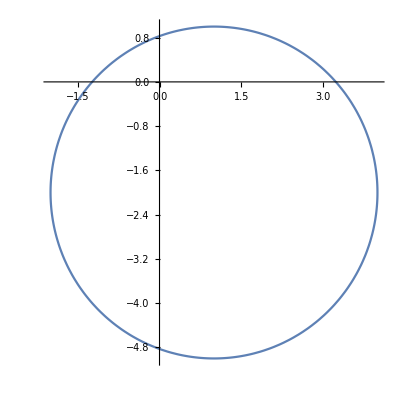

```mathematica
f[t_]={1+3Cos[t],-2+3Sin[t]}
ParametricPlot[f[t],{t,0,2Pi},AspectRatio->Automatic]
```

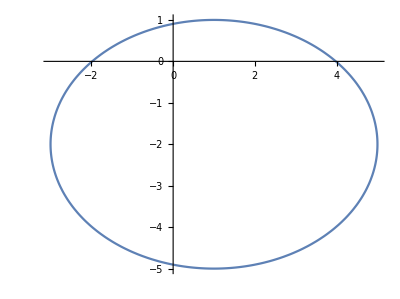

```mathematica
ParametricPlot[{1+4Cos[t],-2+3Sin[t]},{t,0,2Pi},AspectRatio->Automatic]
```

{-1+3 t,2-t}

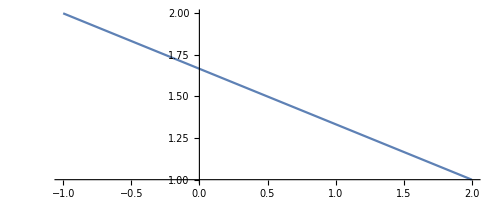

```mathematica
f[t_]={-1,2} + t*({2,1}-{-1,2})
ParametricPlot[f[t],{t,0,1}]
```

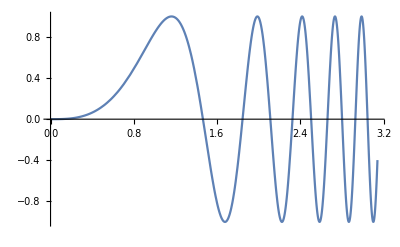

```mathematica
Plot[Sin[x^3],{x,0,Pi}]
```

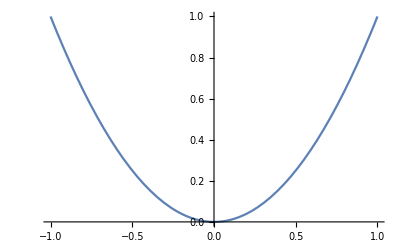

```mathematica
Plot[x^2,{x,-1,1}]
```

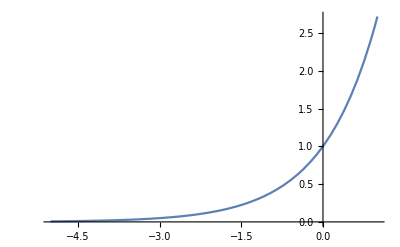

```mathematica
Plot[Exp[x], {x,-5,1}]
```

{t,Sin[t^3]}

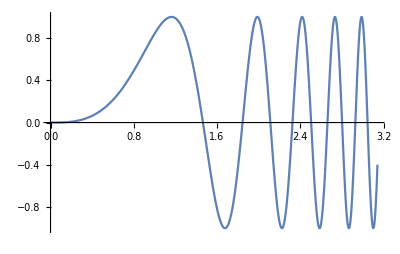

```mathematica
f[t_]={t,Sin[t^3]}
ParametricPlot[f[t],{t,0,Pi}]
```

***Start of exercise 1

{1+4 t,1+t}

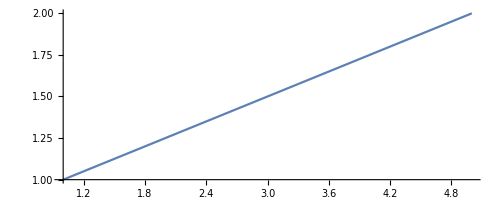

```mathematica
f[t_]={1,1} + t*({5,2}-{1,1})
ParametricPlot[f[t],{t,0,1}]
```

{5+t,2+2 t}

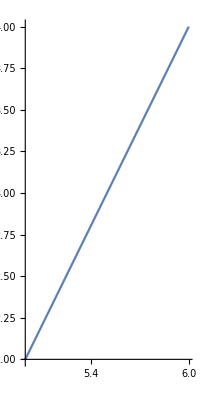

```mathematica
g[t_]={5,2} + t*({6,4}-{5,2})
ParametricPlot[g[t],{t,0,1}]
```

{6-3 t,4+3 t}

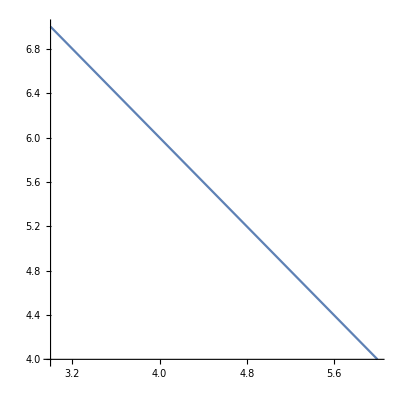

```mathematica
h[t_]={6,4} + t*({3,7}-{6,4})
ParametricPlot[h[t],{t,0,1}]
```

{3,7-2 t}

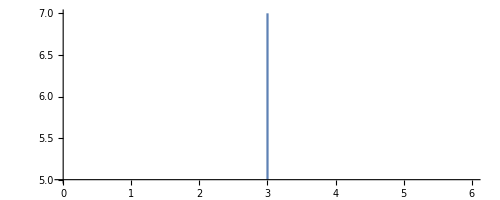

```mathematica
j[t_]={3,7} + t*({3,5}-{3,7})
ParametricPlot[j[t],{t,0,1}]
```

{3-2.5 t,5-t}

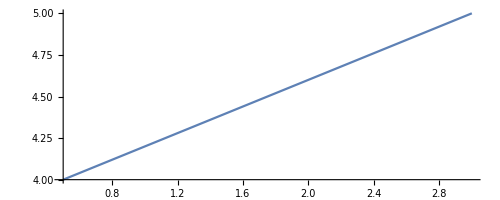

```mathematica
k[t_]={3,5} + t*({0.5,4}-{3,5})
ParametricPlot[k[t],{t,0,1}]
```

```mathematica
graph1 = ParametricPlot[f[t],{t,0,1},AspectRatio->Automatic]
```

-Graphics-

```mathematica
graph2 = ParametricPlot[g[t],{t,0,1},AspectRatio->Automatic]
```

-Graphics-

```mathematica
graph3 = ParametricPlot[h[t],{t,0,1},AspectRatio->Automatic]
```

-Graphics-

```mathematica
graph4 = ParametricPlot[j[t],{t,0,1},AspectRatio->Automatic]
```

-Graphics-

```mathematica
graph5 = ParametricPlot[k[t],{t,0,1},AspectRatio->Automatic]
```

-Graphics-

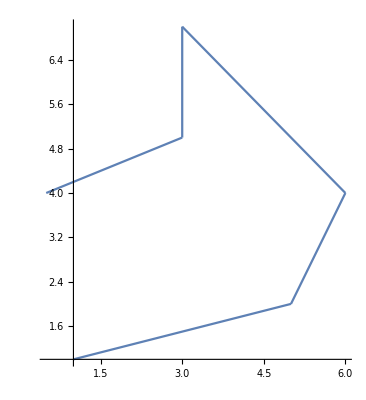

```mathematica
Show[{graph1,graph2,graph3,graph4,graph5},PlotRange->All]
```

although this initially look different than the one in the lab manual it is in fact the same image, it looks different because the axis of the graph start at (1,1) not (0,0).
**** end of exercise 1

```mathematica
f[t_]={Cos[t],Sin[t],0}
circle0=ParametricPlot3D[f[t],{t,0,2Pi}]
```

{Cos[t],Sin[t],0}

-Graphics3D-

```mathematica
circle1=ParametricPlot3D[{Cos[t],Sin[t],1},{t,0,2Pi}]
circle2=ParametricPlot3D[{Cos[t],Sin[t],2},{t,0,2Pi}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[circle2,circle1,circle0]
```

-Graphics3D-

```mathematica
circle=ParametricPlot3D[{Cos[t],0,Sin[t]},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
f[t_]={Cos[t],Sin[t],t/2}
```

{Cos[t],Sin[t],t/2}

```mathematica
ParametricPlot3D[f[t],{t,0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[f[t],{t,0,6Pi}]
```

-Graphics3D-

```mathematica
f[t_]={Cos[2Pi*t],Sin[2Pi*t],t}
```

{Cos[2 π t],Sin[2 π t],t}

```mathematica
ParametricPlot3D[f[t],{t,0,3}]
```

-Graphics3D-

```mathematica
f[t_]={t Cos[2 π t],t Sin[2 π t],2 t};
ParametricPlot3D[f[t],{t,0,10},ViewPoint->{0,-10,1}]
```

-Graphics3D-

Sin[6 π x]

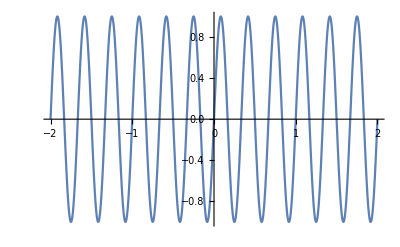

```mathematica
g[x_]=Sin[6Pi x]
Plot[g[x],{x,-2,2}]
```

```mathematica
f[t_]={t,Sin[6Pi t], 0}
ParametricPlot3D[f[t],{t,-2,2},PlotPoints->300]
```

{t,Sin[6 π t],0}

-Graphics3D-

```mathematica
f[t_]={t,Sin[6Pi t], t}
ParametricPlot3D[f[t],{t,-2,2},PlotPoints->300]
```

{t,Sin[6 π t],t}

-Graphics3D-

```mathematica
f[t_]={t,Sin[6Pi t], 4-t}
ParametricPlot3D[f[t],{t,-2,2},PlotPoints->300]
```

{t,Sin[6 π t],4-t}

-Graphics3D-

```mathematica
f[t_]={t,Sin[6Pi t], 4-Abs[t]}
ParametricPlot3D[f[t],{t,-2,2},PlotPoints->300]
```

{t,Sin[6 π t],4-Abs[t]}

-Graphics3D-

```mathematica
f[t_]={t,Sin[6Pi t], t^2}
ParametricPlot3D[f[t],{t,-2,2},PlotPoints->300]
```

{t,Sin[6 π t],t^2}

-Graphics3D-

```mathematica
f[t_]={t,Sin[6Pi t], t^3 / 2}
ParametricPlot3D[f[t],{t,-2,2}]
```

{t,Sin[6 π t],t^3/2}

-Graphics3D-

******Start of exercise 3*******

```mathematica
cyl=ContourPlot3D[x^2+y^2==9,{x,-4,4},{y,-4,4},{z,0,8}]
```

-Graphics3D-

```mathematica
plane1=Plot3D[4-x,{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
Show[cyl,plane1]
```

-Graphics3D-

```mathematica
f[t_]={3Cos[t],3Sin[t],4-3Cos[t]}
```

{3 Cos[t],3 Sin[t],4-3 Cos[t]}

```mathematica
ParametricPlot3D[f[t],{t,0,2Pi}]
```

-Graphics3D-

to make a circle of radius 3 we can change the formula x^2+^2=9
to {3cos(t),3sin(t)} then we just need to parameterize our z component. since z=4-x, and x = 3cos(t)
we can parameterize z=4-3cos(t)
*******end of exercise 3******

******exercise 7******
1 revolution from 0->2pi, 
10 revolutions from 0->20pi,
 20 revolutions from -20pi->20pi
 can alter cos(t) to cos(2Pi*t) that way i can evaluate from -10 to 10 rather than -20pi to 20pi
 
 can divide x(t),y(t),z(t) by 10  to keep bounds from [-1,1] on all axis

```mathematica
f[t_]={t*Cos[2*Pi*t]/10, t*Sin[2*Pi*t]/10,t/10};
ParametricPlot3D[f[t],{t,-10,10}]
```

-Graphics3D-